```mathematica
nsmax=2 10^21;
TLC=2π (Lct C0t)^(1/2);

DensPlot[tframe_]:=
Show[{
LogPlot[{nn0z[zct z]/nn0t(*,nnout[zct z,tframe]/nn0t*)},{z,0,1},PlotRange->{0.0005,20},PlotStyle->{{Gray}}],
ListLogPlot[MovingAverage[Table[{z,nnout[zct z,tframe]/nn0t},{z,0,1,0.01}],4],PlotRange->{0.0005,30},PlotStyle->{{Gray,Dashed,Thickness[0.01]}},Joined->True],
LogPlot[{nsout[tframe]UnitStep[z-zsout[tframe]/zct]UnitStep[zsout[tframe]/zct+wsout[tframe]/zct-z]/nn0t,0.0001},{z,0,1},PlotStyle->Purple,Filling->{1->{2}},FillingStyle->{Opacity[nsout[tframe]/nsmax/1.5]}],
ListLogPlot[{{ zsout[tframe]/zct,10^17/nn0t},{zsout[tframe]/zct,nsout[tframe]/nn0t}},Joined->True,PlotStyle->{Black,Thickness[0.008]}],
ListLogPlot[{{ zsout[tframe]/zct+wsout[tframe]/zct,10^17/nn0t},{zsout[tframe]/zct+wsout[tframe]/zct,nsout[tframe]/nn0t}},Joined->True,PlotStyle->{Black,Thickness[0.008]}],
ListLogPlot[{{zsout[tframe]/zct,nsout[tframe]/nn0t},{zsout[tframe]/zct+wsout[tframe]/zct,nsout[tframe]/nn0t}},Joined->True,PlotStyle->{Black,Thickness[0.008]}]
},
Frame->True,
FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],
AspectRatio->1,
ImageSize->300,
(*FrameLabel->{"Distance, z/z_c","Density, n_j/n_(n, 0)"},*)
FrameLabel->None,
AxesLabel->None,
Axes->False,
(*LabelStyle->{18,Black},*)
AxesLabel->None,
FrameStyle->Thickness[0.008],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}
]
```

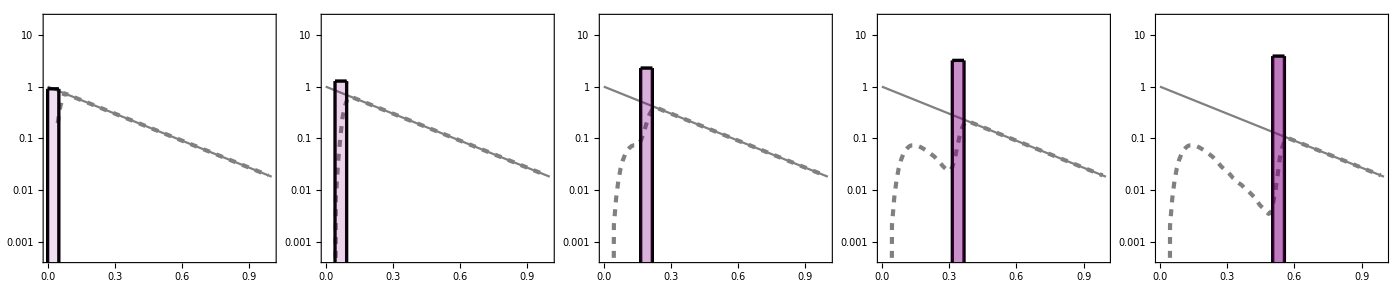

```mathematica
GraphicsGrid[{Table[DensPlot[j TLC],{j,0,0.2,0.05}]},ImageSize->1400,Spacings->-10]
```

```mathematica
DensPlot[tframe_]:=
Show[{
LogPlot[{nn0z[zct z]/nn0t(*,nnout[zct z,tframe]/nn0t*)},{z,0,1},PlotRange->{0.0005,20},PlotStyle->{{Thin,Gray},{Gray,Dashed}}],
ListLogPlot[MovingAverage[Table[{z,nnout[zct z,tframe]/nn0t},{z,0,1,0.01}],4],PlotRange->{0.0005,30},PlotStyle->{{Gray,Dashed}},Joined->True],
LogPlot[{nsout[tframe]UnitStep[z-zsout[tframe]/zct]UnitStep[zsout[tframe]/zct+wsout[tframe]/zct-z]/nn0t,0.0001},{z,0,1},PlotStyle->Purple,Filling->{1->{2}},FillingStyle->{Opacity[nsout[tframe]/nsmax/1.5]}],
ListLogPlot[{{ zsout[tframe]/zct,10^17/nn0t},{zsout[tframe]/zct,nsout[tframe]/nn0t}},Joined->True,PlotStyle->Black],
ListLogPlot[{{ zsout[tframe]/zct+wsout[tframe]/zct,10^17/nn0t},{zsout[tframe]/zct+wsout[tframe]/zct,nsout[tframe]/nn0t}},Joined->True,PlotStyle->Black],
ListLogPlot[{{zsout[tframe]/zct,nsout[tframe]/nn0t},{zsout[tframe]/zct+wsout[tframe]/zct,nsout[tframe]/nn0t}},Joined->True,PlotStyle->Black]
},
Frame->True,
AspectRatio->1,
ImageSize->300,
FrameLabel->{"Distance, z/z_c","Density, n_j/n_(n, 0)"},
FrameLabel->None,
AxesLabel->None,
Axes->False,
LabelStyle->{18,Black},
AxesLabel->None,
FrameStyle->Thickness[0.006],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}
]
```

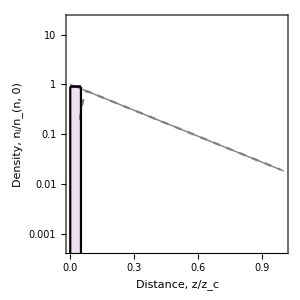

```mathematica
DensPlot[0 TLC]
```